```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
VertexCount[g]==6&&ConnectedGraphQ[g]&&IsomorphicGraphQ[VertexDelete[g,6],CycleGraph[5]
&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]]
]&]
```

{5039856,5039859,5039860,5039857,5039829,5039832,5039833,5039830,5039127,5039130,5039131,5039128,5039100,5039103,5039104,5039101,4980807,4980810,4980811,4980808,4980780,4980783,4980784,4980781,4980078,4980081,4980082,4980079,4980054,4980055,4980052}

```mathematica
Table[ShowGraph[allGraphs6,k],{k,%}]
```

{-Graphics-5039856,-Graphics-5039859,-Graphics-5039860,-Graphics-5039857,-Graphics-5039829,-Graphics-5039832,-Graphics-5039833,-Graphics-5039830,-Graphics-5039127,-Graphics-5039130,-Graphics-5039131,-Graphics-5039128,-Graphics-5039100,-Graphics-5039103,-Graphics-5039104,-Graphics-5039101,-Graphics-4980807,-Graphics-4980810,-Graphics-4980811,-Graphics-4980808,-Graphics-4980780,-Graphics-4980783,-Graphics-4980784,-Graphics-4980781,-Graphics-4980078,-Graphics-4980081,-Graphics-4980082,-Graphics-4980079,-Graphics-4980054,-Graphics-4980055,-Graphics-4980052}

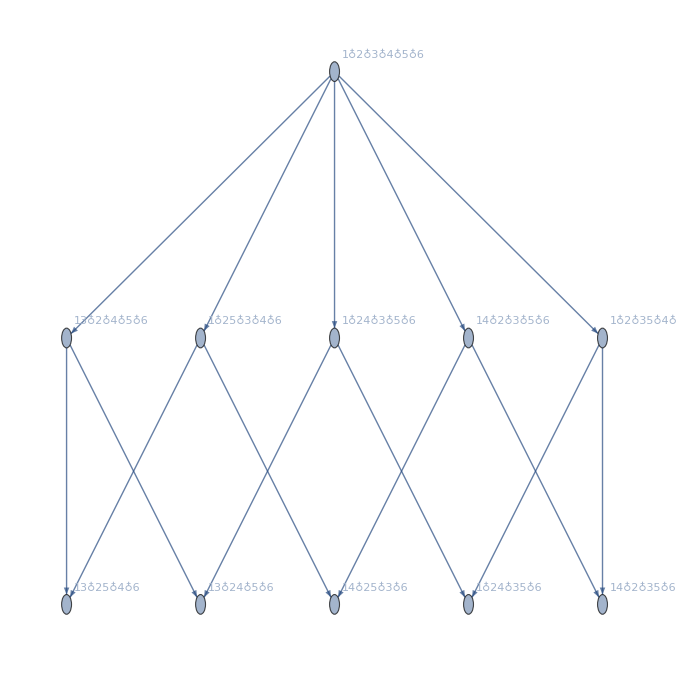

```mathematica
FormulaGraph[allGraphs6[5039860, "colofour"]]
```

```mathematica
ff=FindFullFormula[VertexDelete[Graph[plantri[[1]]],1]]
```

{v2x3x4x5x6x7x8x9xaxbxc,v2x3x4x5x6x7x8x9bxaxc,v2x3x4x5x6x7x8bx9xaxc,v2x3x4x5x6x7x8ax9xbxc,v2x3x4x5x6x7x8ax9bxc,v2x3x4x5x6x7ax8x9xbxc,v2x3x4x5x6x7ax8x9bxc,v2x3x4x5x6x7ax8bx9xc,v2x3x4x5x6x79x8xaxbxc,v2x3x4x5x6x79x8bxaxc,v2x3x4x5x6x79x8axbxc,v2x3x4x5x6cx7x8x9xaxb,v2x3x4x5x6cx7x8x9bxa,v2x3x4x5x6cx7x8bx9xa,v2x3x4x5x6cx7x8ax9xb,v2x3x4x5x6cx7x8ax9b,v2x3x4x5x6cx7ax8x9xb,v2x3x4x5x6cx7ax8x9b,v2x3x4x5x6cx7ax8bx9,7466,v24cx357x68ax9b,v24x35x68x7ax9xbxc,v24x35cx68x7ax9xb,v24cx35x68x7ax9xb,v24bx35x68x7ax9xc,v24bx35cx68x7ax9,v24x35x68x7ax9bxc,v24x35cx68x7ax9b,v24cx35x68x7ax9b,v24x35x68x79xaxbxc,v24x35cx68x79xaxb,v24cx35x68x79xaxb,v24bx35x68x79xaxc,v24bx35cx68x79xa,v24x35x68ax79xbxc,v24x35cx68ax79xb,v24cx35x68ax79xb,v24bx35x68ax79xc,v24bx35cx68ax79}
 |  |  |  |

```mathematica
Signature12[s_]:=First[Map[Select[Map[Intersection[#,{2,3,4,5,6}]&,#],#≠{}&]&,Map[SymbolToSets,{s}]]]
```

```mathematica
Signature12[v2x3x4x5x6x7x8x9xaxbxc]
```

{{2},{3},{4},{5},{6}}

```mathematica
RemoveThem[sets_]:=Select[Map[Select[#,!MemberQ[{2,3,4,5,6},#]&]&,sets],#≠{}&]
```

```mathematica
RemoveThem[SymbolToSets[v2x3x4x5x6x7x8x9xaxbxc]]
```

{{7},{8},{9},{10},{11},{12}}

```mathematica
dd1=Map[RemoveThem[SymbolToSets[#]]&,Select[ff,With[{s=Signature12[#]}, s=={{2},{3,5},{4},{6}}]&]]//Tally//Sort;
```

```mathematica
dd2=Map[RemoveThem[SymbolToSets[#]]&,Select[ff,With[{s=Signature12[#]}, s=={{2},{3},{4,6},{5}}]&]]//Tally//Sort;
```

```mathematica
Intersection[dd1,dd2]//Length
```

65

```mathematica
Select[ff,With[{s=Signature12[#]},s=={{2},{3},{4,6},{5}}]&]//Length
```

760

```mathematica
Sort[DeleteDuplicates [Select[Map[Select[Map[Intersection[#,{2,3,4,5,6}]&,#],#≠{}&]&,Map[SymbolToSets,ff]],Length[#]≤4&]]]
```

{{{2},{3,5},{4,6}},{{2,4},{3,5},{6}},{{2,4},{3,6},{5}},{{2,5},{3},{4,6}},{{2,5},{3,6},{4}},{{2},{3},{4,6},{5}},{{2},{3,5},{4},{6}},{{2},{3,6},{4},{5}},{{2,4},{3},{5},{6}},{{2,5},{3},{4},{6}}}

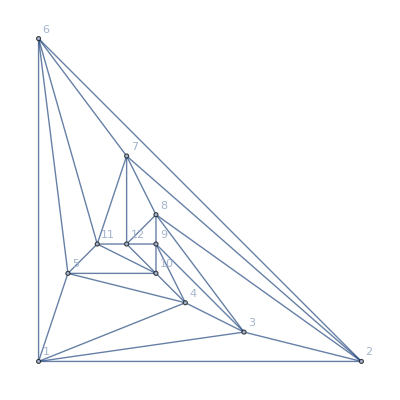

```mathematica
Graph[plantri[[1]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

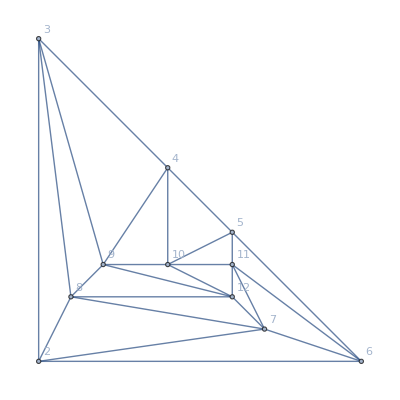

```mathematica
VertexDelete[Graph[plantri[[1]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"],1]
```